```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_CRIX/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.30605,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.016646,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | CRIX Price | log return future | log return CRIX
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 4387.15 | 0.0212907 | 0.0333146
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 4243.4 | -0.0904653 | -0.157294
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 4966.22 | -0.0196938 | -0.0120673
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 5026.51 | -0.131645 | -0.123533
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 5687.44 | 0.03685 | 0.0547603
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 5384.37 | -0.119603 | -0.109093
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 6005. | -0.042369 | -0.0285305
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 6178.8 | 0.018947 | 0.0208764
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 6051.14 | -0.0359909 | 0.003586)

```mathematica
data[[1,7]]
```

log return CRIX

```mathematica
data[[1,6]]
```

log return future

```mathematica
tmp=Import[NotebookDirectory[] <> "data_CRIX/" <> ToString[kk] <> "_parameters.csv"]
```

(2021-05-20
0.888306
0.0411777
0.858678)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_CRIX/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.0562189 | 0.0264995
0.0125597 | 0.0124398
0.433291 | 0.414652
0.47661 | 0.444351
0.906222 | 0.904282
0.943801 | 0.955421
0.971421 | 0.968041
0.50783 | 0.467051
0.752885 | 0.771485
0.9894 | 0.9902)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.073061,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.962904,0.44316,1.44255,9.98964,0.808509}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{2.68129,4.48794,3.55185,4.76972,3.49638}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.671109,0.00970492,0.192646,0.0157934,0.817216}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.66772,0.0136079,0.187202,0.0116803,0.812511}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

397.143

```mathematica
%/Length[data]
```

1.31941

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {3.7854}. NIntegrate obtained 0.000113669 and 8.18197×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {3.197}. NIntegrate obtained 0.00141832 and 1.92348×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.63141}. NIntegrate obtained 0.0999181 and 1.9×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{16.6776,424.45}

```mathematica
%/Length[data]
```

{0.0554074,1.41013}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=87, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
tmp=Import[NotebookDirectory[] <> "data_CRIX/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {3.7854}. NIntegrate obtained 0.000113669 and 8.18197×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {3.197}. NIntegrate obtained 0.00141832 and 1.92348×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.63141}. NIntegrate obtained 0.0999181 and 1.9×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
tLLnew={};
mLLnew={};
For[kk=0, kk<=87, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
uv=Import[NotebookDirectory[] <> "data_CRIX/" <> ToString[kk] <> "_simulation.csv"];
skd=SmoothKernelDistribution[uv];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLnew, ll];
AppendTo[mLLnew,mll];
]
```

```mathematica
tLL
```

{424.45,435.002,474.241,480.315,406.632,449.318,454.126,449.452,459.14,457.748,474.84,467.424,465.073,460.84,462.509,482.244,480.143,493.753,407.625,480.323,487.637,523.26,484.694,519.812,492.515,502.225,491.298,509.646,525.761,509.302,521.722,519.605,522.462,523.588,532.201,547.106,551.885,556.504,560.834,524.638,550.812,510.517,517.707,519.577,538.179,534.404,534.936,531.482,528.322,522.123,516.863,508.476,512.285,513.337,506.04,498.549,499.097,493.612,486.352,464.498,466.592,465.648,458.703,461.355,450.974,456.682,449.613,442.618,432.883,433.443,428.236,422.406,421.453,403.17,407.443,401.67,400.945,405.762,391.864,382.915,384.676,382.784,383.128,385.614,394.098,399.573,391.735,395.115}

```mathematica
tLLnew
```

{397.143,397.636,396.91,400.601,407.299,405.534,406.456,410.23,413.927,413.777,410.327,416.016,413.795,413.589,419.835,421.679,425.67,421.158,429.215,421.899,426.365,417.905,423.096,411.713,420.197,416.38,420.189,420.272,416.144,420.519,409.935,408.087,411.1,415.292,421.213,425.144,425.563,423.347,421.736,421.913,424.203,425.044,416.589,411.023,407.149,401.358,401.72,401.442,400.676,396.747,392.799,389.457,389.933,392.859,389.16,385.794,388.354,383.488,384.204,371.068,369.472,368.394,363.964,363.836,353.806,367.313,361.532,355.635,353.502,352.08,343.704,341.194,340.549,337.862,328.609,322.996,326.315,327.757,326.564,325.439,322.513,324.051,323.245,311.924,317.557,321.002,323.435,319.281}

```mathematica
Min[tLL-tLLnew]
```

15.7975

```mathematica
mLL
```

{1.41013,1.44519,1.57555,1.59573,1.35094,1.49275,1.50873,1.4932,1.52538,1.52076,1.57754,1.55291,1.54509,1.53103,1.53658,1.60214,1.59516,1.64038,1.35424,1.59576,1.62006,1.73841,1.61028,1.72695,1.63626,1.66852,1.63222,1.69318,1.74671,1.69203,1.7333,1.72626,1.73575,1.7395,1.76811,1.81763,1.83351,1.84885,1.86324,1.74298,1.82994,1.69607,1.71996,1.72617,1.78797,1.77543,1.7772,1.76572,1.75522,1.73463,1.71715,1.68929,1.70194,1.70544,1.6812,1.65631,1.65813,1.63991,1.61579,1.54318,1.55014,1.547,1.52393,1.53274,1.49825,1.51722,1.49373,1.47049,1.43815,1.44001,1.42271,1.40334,1.40018,1.33943,1.35363,1.33445,1.33204,1.34805,1.30187,1.27214,1.27799,1.27171,1.27285,1.28111,1.30929,1.32748,1.30144,1.31268}

```mathematica
mLLnew
```

{1.31941,1.32105,1.31864,1.3309,1.35315,1.34729,1.35035,1.36289,1.37517,1.37467,1.36321,1.38211,1.37473,1.37405,1.3948,1.40093,1.41419,1.3992,1.42596,1.40166,1.4165,1.38839,1.40563,1.36782,1.396,1.38332,1.39598,1.39625,1.38254,1.39707,1.36191,1.35577,1.36578,1.37971,1.39938,1.41244,1.41383,1.40647,1.40112,1.4017,1.40931,1.41211,1.38402,1.36553,1.35266,1.33342,1.33462,1.33369,1.33115,1.31809,1.30498,1.29388,1.29546,1.30518,1.29289,1.28171,1.29021,1.27405,1.27642,1.23278,1.22748,1.2239,1.20918,1.20876,1.17544,1.22031,1.2011,1.18151,1.17443,1.1697,1.14187,1.13353,1.13139,1.12246,1.09172,1.07308,1.0841,1.08889,1.08493,1.08119,1.07147,1.07658,1.0739,1.03629,1.05501,1.06645,1.07453,1.06073}

```mathematica
Export[NotebookDirectory[] <> "data/LL_NIG.csv", Prepend[{Range[0,87],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/LL_NIG.csv

```mathematica
Export[NotebookDirectory[] <> "data/LL_NIG_new.csv", Prepend[{Range[0,87],tLLnew, mLLnew}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/LL_NIG_new.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

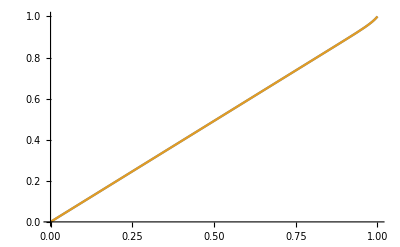

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

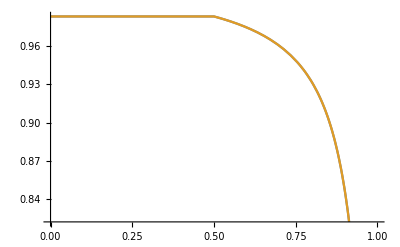

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

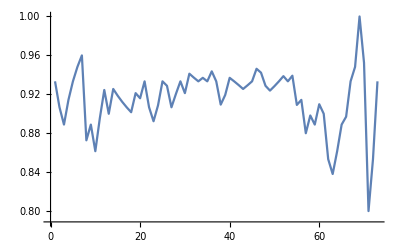

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

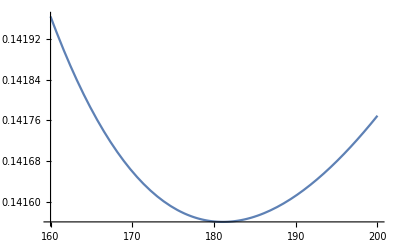

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```